## ZProjection-Example.nb

```mathematica
<<Cellzilla2D.m
```

Cellzilla2D (3.0.51e (11 June 2017)) loaded Tue 13 Jun 2017 12:56:36
using xCellerator 0.95 and XSSA 1.3.2
GPL License Terms Apply

```mathematica
T=CSVToTissue["3DMeristem.csv"]
```

Tissue[{{-71.1111,-67.7811,1.68},{-71.3813,-66.5817,1.68},{-71.5425,-65.3221,1.68},{-71.6249,-64.0423,1.68},{-71.6609,-62.7632,1.68},{-71.6744,-61.4917,1.68},{-71.6787,-60.2282,1.68},{-71.6797,-58.9708,1.68},{-71.68,-57.7172,1.68},2348,{12.452,3.0018,34.9943},{18.2967,-8.6356,33.7247},{32.3821,-9.01383,29.0773},{36.3476,12.275,27.4857},{42.5031,17.9056,21.8844},{40.0075,11.4681,25.757},{-3.42352,-22.3926,29.1375},{-1.65751,-3.93387,34.7489}},{1},{1}]
 |  |  |  |

```mathematica
Q=ZProjection[T]
```

Tissue[{{-71.1111,-67.7811},{-71.3813,-66.5817},{-71.5425,-65.3221},{-71.6249,-64.0423},{-71.6609,-62.7632},2355,{36.3476,12.275},{42.5031,17.9056},{40.0075,11.4681},{-3.42352,-22.3926},{-1.65751,-3.93387}},{1},{1}]
 |  |  |  |

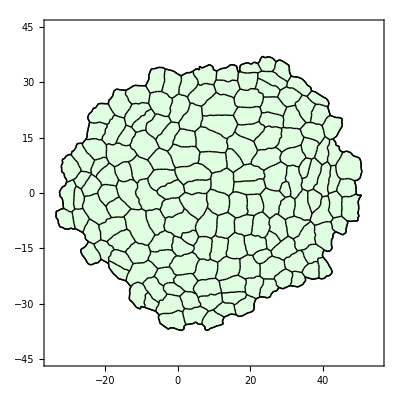

```mathematica
ShowTissue[Q, Frame-> True, PlotRange-> {{-35,55},{-45,45}}, ImageSize-> 400]
```

```mathematica
ShowZProjection[T, Frame-> True, PlotRange-> {{-35,55},{-45,45}}, ImageSize-> 400]
```

-Graphics-